## Fixed points

### Initialization

Try to model exactly the solution for two cells.
v2: modular approach

```mathematica
Clear["Global`*"];
```

```mathematica
S[x_]:= Coff +(Con-Coff)*x;
g[x1_,x2_]:= S[x1] + fd*S[x2];
RSolve[{x1[t+1] == g[x1[t], x2[t]]^n/(k^n+g[x1[t], x2[t]]^n),x2[t+1] == g[x2[t], x1[t]]^n/(k^n+g[x2[t], x1[t]]^n), x1[0]==x1i, x2[0]==x2i} /. {n-> 1}, {x1[t],x2[t]},t]
```

RSolve[{x1[1+t]==(Coff+(-Coff+Con) x1[t]+fd (Coff+(-Coff+Con) x2[t]))/(Coff+k+(-Coff+Con) x1[t]+fd (Coff+(-Coff+Con) x2[t])),x2[1+t]==(Coff+fd (Coff+(-Coff+Con) x1[t])+(-Coff+Con) x2[t])/(Coff+k+fd (Coff+(-Coff+Con) x1[t])+(-Coff+Con) x2[t]),x1[0]==x1i,x2[0]==x2i},{x1[t],x2[t]},t]

Typical value of f(d):

```mathematica
a0val = 1.5;
fdval = Exp[R-a0]/a0 Sinh[R] /. {R-> 0.1, a0-> a0val};
params = {k-> 13, Coff-> 1, Con-> 28, fd-> fdval, n-> 2};
```

### Fixed points (exact)

For n = 2 we can obtain exact solutions from the solution of the cubic equation.

```mathematica
Solve[{0== g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,0 == g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2} /. {n-> 2}, {x1,x2}]
```

$Aborted

```mathematica
red =Reduce[(0== g[x1, x2]^n/(k^n+g[x1, x2]^n) -x1&&0 == g[x2, x1]^n/(k^n+g[x2, x1]^n) -x2)/. {n-> 2}, {x1,x2}]
```

$Aborted

```mathematica
For[i=1, i≤ Length[red],i++, Print[red[[i]] ] ]
```

Con==0&&Coff==0&&-k+fd^2 k≠0

fd==-1&&Coff==Con&&k≠0

fd==1&&Con==0&&Coff==0&&k≠0

(fd==-1||fd==1)&&Coff-Con≠0&&x2==(Coff+Coff fd-Coff fd x1+Con fd x1)/(Coff-Con)&&k≠0

(Coff-Con) (-1+fd^2)≠0&&x1==Coff/(Coff-Con)&&x2==(Coff+Coff fd-Coff fd x1+Con fd x1)/(Coff-Con)&&k≠0

Special case X1 = X2

```mathematica
Solve[{0== g[x, x]^n/(k^n+g[x, x]^n)-x} /. {n-> 2}, {x}]
```

$Aborted

Rewrite equation into
 -(C_on-1)^2 X^3+[(C_on-1)^2 -2 (C_on-1)]X^2 + [2(C_on-1) - 1 - K^2/((1 + f(d))^2)]X + 1 =0

Δ = 18 a b c d - 4 b^3 d + b^2 c^2 - 4 a c^3 - 27 a^2 d^2;
Δ > 0: three distinct roots

```mathematica
a=  -(Con-1)^2;
b = (Con-1)^2 -2 (Con-1);
c =  2(Con-1) - 1 - k^2/((1 + fd)^2);
d = 1;
Δ = 18 a b c d - 4 b^3 d + b^2 c^2 - 4 a c^3 - 27 a^2 d^2;
Apart[Δ]
```

-(4 (-1+Con)^2 Con^3 k^2)/(1+fd)^2+((-1+Con)^2 (-27+18 Con+Con^2) k^4)/(1+fd)^4-(4 (-1+Con)^2 k^6)/(1+fd)^6

```mathematica
Solve[Δ == 0, fd, Reals]
```

{{fd→ConditionalExpression[Root[4 Con^3+27 k^2-18 Con k^2-Con^2 k^2+4 k^4+(16 Con^3+54 k^2-36 Con k^2-2 Con^2 k^2) #1+(24 Con^3+27 k^2-18 Con k^2-Con^2 k^2) #1^2+16 Con^3 #1^3+4 Con^3 #1^4&,1],Con>9||Con<0]},{fd→ConditionalExpression[Root[4 Con^3+27 k^2-18 Con k^2-Con^2 k^2+4 k^4+(16 Con^3+54 k^2-36 Con k^2-2 Con^2 k^2) #1+(24 Con^3+27 k^2-18 Con k^2-Con^2 k^2) #1^2+16 Con^3 #1^3+4 Con^3 #1^4&,2],Con>9||Con<0]},{fd→ConditionalExpression[Root[4 Con^3+27 k^2-18 Con k^2-Con^2 k^2+4 k^4+(16 Con^3+54 k^2-36 Con k^2-2 Con^2 k^2) #1+(24 Con^3+27 k^2-18 Con k^2-Con^2 k^2) #1^2+16 Con^3 #1^3+4 Con^3 #1^4&,3],Con>9]},{fd→ConditionalExpression[Root[4 Con^3+27 k^2-18 Con k^2-Con^2 k^2+4 k^4+(16 Con^3+54 k^2-36 Con k^2-2 Con^2 k^2) #1+(24 Con^3+27 k^2-18 Con k^2-Con^2 k^2) #1^2+16 Con^3 #1^3+4 Con^3 #1^4&,4],Con>9]}}

Note that Δ is a quintic equation in C_on, therefore it is not easy to find the roots of Δ=0 which gives the range where we have three real solutions.

### Fixed points (numerical)

If there exists a solution, it appears to be unique. However, it seems that Mathematica is only able to find solutions for specific values of n (e.g. n=1, 2, 1.5, 1.2)

Try out solution

```mathematica
params = {k-> 10, Coff-> 1, Con-> 15, fd-> fdval, n-> 2};
NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals} /. params, {x1,x2}]
```

{{x1→0.0211611,x2→0.0211611}}

Plot against Con

```mathematica
params = {k-> 10, Coff-> 1,fd->fdval, n-> 2};
del = 0.2;
nsol=Table[
NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals, 0≤x1≤1, 0≤x2≤1 } /. params /.{Con-> c}, {x1,x2}],{c,1,30,del}];
```

Process data to get all solutions

```mathematica
lvals1=Length/@(x1/.nsol);
t=Table[ ConstantArray[1+(i-1)*del, lvals1[[i]]], {i, 1, Length[lvals1]}] ;
pvals1=Flatten[Transpose/@Transpose[{t,x1/.nsol}], {1,2}];
```

Compare with Δ of cubic equation (n=2)

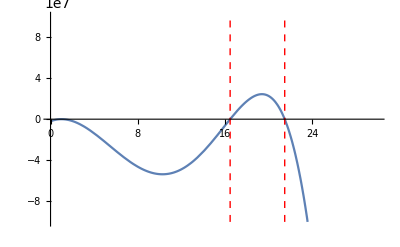

```mathematica
sol = NSolve[(Δ/.{k-> 10, Coff-> 1,fd->fdval}) ==0 && Con>1, Con];
linestyle={Red, Thick, Dashed};
line1 = Line[{{Con/.sol[[1]], -10^8},{Con/.sol[[1]],10^8}}];
line2 = Line[{{Con/.sol[[2]],-10^8},{Con/.sol[[2]],10^8}}];
p0a = Plot[Δ/.{k-> 10, Coff-> 1,fd->fdval}, {Con, 0, 30}, PlotRange-> {{0, 30}, {-10^8, 10^8}}, Epilog->{Directive[linestyle],line1,line2}]
```

Plot together

```mathematica
linestyle={Red, Thick, Dashed};
line1 = Line[{{Con/.sol[[1]], 0},{Con/.sol[[1]],1}}];
line2 = Line[{{Con/.sol[[2]],0},{Con/.sol[[2]],1}}];
```

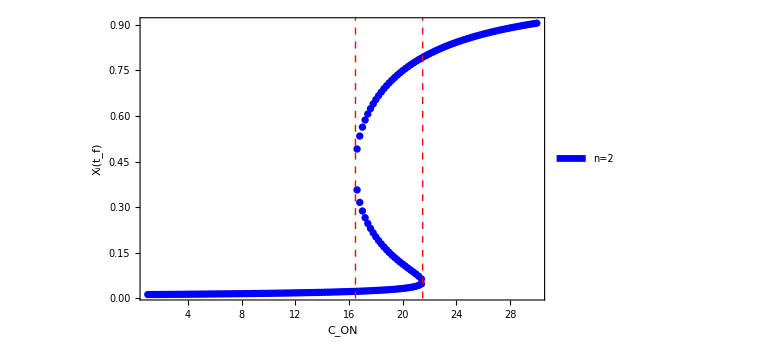

```mathematica
fstyle = Style[#,16] & ;
l1 = Placed[SwatchLegend[fstyle/@{"n=2"}, LegendMarkerSize->10],Above]; 
p1=ListPlot[pvals1, PlotStyle-> {Blue}, AxesLabel-> {"C_ON", "X_i(t_f)"}, PlotLegends-> l1 ];
fig2=Show[p1,ImageSize-> Large,BaseStyle-> {FontSize-> 20}, Frame-> True, FrameLabel-> {"C_ON", "X_i(t_f)"}, PlotRange-> All,Epilog->{Directive[linestyle],line1,line2}]
```

Export figure

```mathematica
name = "steady_state_vs_Con_k_10_Coff_1_fd_0p13_fN_1p5_n_var.pdf";
fname = FileNameJoin[{NotebookDirectory[], "finite_Hill_two_cells", name}];
(*Export[fname,fig2]*)
```

H:\My Documents\Multicellular automaton\Mathematica calculations\finite_Hill_homogenisation\steady_state_vs_Con_k_10_Coff_1_fd_0p13_fN_1p5_n_var.pdf

Plot against K

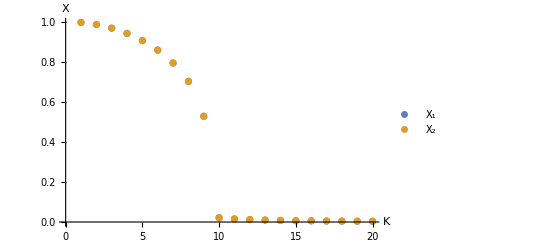

```mathematica
nsol=Table[
First@NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals} /. {k-> c, Coff-> 1, Con->15, fd->fdval, n->2}, {x1,x2}], {c,1,20}];
ListPlot[{x1/.nsol, x2/.nsol}, AxesLabel-> {"K", "X"}, PlotLegends-> {"X_1","X_2"}]
```

Plot against fN

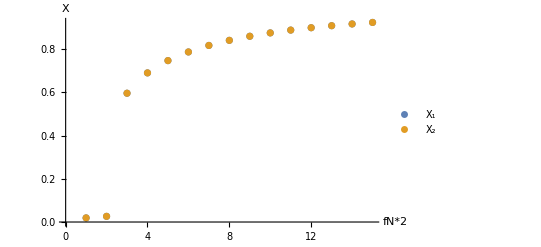

```mathematica
nsol=Table[
First@NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals} /. {k-> 10, Coff-> 1, Con->15, fd->c, n-> 2}, {x1,x2}], {c,0.1, 1.5, 0.1}];
ListPlot[{x1/.nsol, x2/.nsol}, AxesLabel-> {"fN*2", "X"}, PlotLegends-> {"X_1","X_2"}]
```

### Fixed point properties

Calculate Jacobian matrix. General expression for eigenvalues is not useful.

```mathematica
J=FullSimplify/@{{D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x1],D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x2]},{ D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x1],D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x2]}};
J  // MatrixForm
```

(-1-((Coff-Con) k^n n (Coff (1+fd-x1-fd x2)+Con (x1+fd x2))^(-1+n))/((k^n+(Coff (1+fd-x1-fd x2)+Con (x1+fd x2))^n)^2) | -((Coff-Con) fd k^n n (Coff (1+fd-x1-fd x2)+Con (x1+fd x2))^(-1+n))/((k^n+(Coff (1+fd-x1-fd x2)+Con (x1+fd x2))^n)^2)
-((Coff-Con) fd k^n n (Coff (1+fd-fd x1-x2)+Con (fd x1+x2))^(-1+n))/((k^n+(Coff (1+fd-fd x1-x2)+Con (fd x1+x2))^n)^2) | -1-((Coff-Con) k^n n (Coff (1+fd-fd x1-x2)+Con (fd x1+x2))^(-1+n))/((k^n+(Coff (1+fd-fd x1-x2)+Con (fd x1+x2))^n)^2))

Calculate fixed points

```mathematica
nsol=NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals} /. params, {x1,x2}]
```

{{x1→0.703288,x2→0.0205994},{x1→0.706284,x2→0.163897},{x1→0.0205994,x2→0.703288},{x1→0.163897,x2→0.706284},{x1→0.717081,x2→0.717081},{x1→0.211574,x2→0.012055},{x1→0.012055,x2→0.211574},{x1→0.199244,x2→0.199244},{x1→0.00960107,x2→0.00960107}}

Numerically calculate eigenvalues at the fixed points. Verify that they are stable (Re[λ] < 0 for all λ).

```mathematica
Jn =FullSimplify[J  /. params];
(* Show Jacobian*) TableForm@Table[ Jn /. nsol[[i]] // MatrixForm, {i, 1, Length[nsol]}]; 
ev=Table[ Eigenvalues[Jn  /. nsol[[i]]], {i, 1, Length[nsol]}];
stability = MapThread[And, Transpose@Negative[ev]];
Print["Eigenvalues negative? (Stable)"];
TableForm[stability, TableHeadings->{Table[StringReplace["Eigenvector number = %d", "%d" ->  ToString[i]], {i,1,Length[nsol]}], {"Positive?"}}]
```

Eigenvalues negative? (Stable)

Eigenvector number = 1 | True
Eigenvector number = 2 | False
Eigenvector number = 3 | True
Eigenvector number = 4 | False
Eigenvector number = 5 | True
Eigenvector number = 6 | False
Eigenvector number = 7 | False
Eigenvector number = 8 | False
Eigenvector number = 9 | True